10.05.2025

## Equations of Motion

### Euler-Lagrange

Th Euler-Lagrange equation describes how particles move in  a field. They include the particle’s position x, its velocity ẋ, and the action given by the Lagrangian L. Here we are concerned with V1 which applies to Newtonian physics where position x and time t are independent.

### Euler-Lagrange V 1

Let L: ℝ^n×ℝ^n→ℝ be differentiable on a region Ω⊂ℝ^(n×n) with L[x,y]=0 for large arguments. Here is the idea: The function x:ℝ->ℝ^n describes the itinerary of one or many particles, ẋ:ℝ->ℝ^n their velocity. The function L is called the Lagrangian. L[x,ẋ] is interpreted as the action that occurs when a particle moves with velocity ẋ at position x. The physical quantities of force and momentum are defined in terms of L as:

F=∂_x L          (force)
P=∂_(ẋ) L       (momentum)

The action is given by :

A[x]=∫_a^b L[x[t],ẋ[t]]ⅆt

and the task is to find an itinerary x that minimizes the action A[x]. The Euler-Lagrange equation, or equation of motion, in its simplest form is:

∂_x L=∂_t ∂_(ẋ) L

or “force = time derivative of momentum”:

F=Ṗ

Solution of (DisplayFormulaNumbered) are stationary points of the problem of the minimizing of the action (DisplayFormulaNumbered).

#### Observations

Every local minimum of A is a stationary point (a solution of Euler-Lagrange), but the reverse is not true. 
A stationary point can be:

a local minimum (second derivative of A positive definite)

a local maximum (second derivative of A negative definite)

a saddle-point (second derivative of A indefinite)

You can do a lot to the Lagrangian without affecting the stationary points:

adding or subtracting a constant

multiplying with a constant

adding a gradient, because the integral over a gradient is a path-independent constant:

A[x]=∫_a^b L[x[t],ẋ[t]]+ ∂f[ẋ[t]]ⅆt  = ∫_a^b L[x[t],ẋ[t]]ⅆt +(f[b]-f[a])

So, a stationary point is, emphatically, only a necessary condition for a local minimum. Conditions o the second derivative of the action A allow us to identify local minima, but need empirical evidence to achieve certainty.

### Newtonian Fields

Let T[ẋ] be the kinetic energy and V[x] the potential energy (or potential) of a particle travelling at position x with velocity ẋ. The Lagrangian is:

L[x,ẋ]=T[ẋ]-V[x]

with:

F:= ∂_x L=-∂V       (force)
P:=∂_(ẋ) L =∂T             (momentum)

Note that force and momentum are defined in terms of the Lagrangian. In classical physics, the kinetic energy is always:

T[ẋ]=1/2 m (ẋ)^2,∂T[ẋ]=m x^(..)

where m is the particle’s mass, so, the equation of motion boils down to:

m x^(..)=F

#### Constant Force, Free Fall

With F= -∂V =const we get:

m x^(..)=const

With F=0, this is Newton’s first law: “if there is no force, acceleration is zero and velocity is constant.” In the case of free fall down the x_2-axis, we have:

m x^(..)=-(0
m g)

or

x^(..)=(0
- g)

#### Harmonic Oscillator

Force is proportional to the deflection (spring, pendulum)

V =k/2 x^2
F= -∂V=-k x

which gives:

m x^(..)=-k x

Setting ω^2=k/m, we get the solution:

x[t]=a Cos[ω t]+b Sin[ω t]

#### Electric Fields

The Lagrangian is

L[x,ẋ]=1/2 m(ẋ)^2+e V[x]

where V:ℝ^3→ℝ is the electric potential, m the mass and e the charge of the moving particle. The force F exerted on a particle of charge e is

F=-e ∂V

The Euler - Lagrange equation for electric fields is

m x^(..)=-e ∂V

#### Work along a Gradient

Let f:ℝ^n→ℝ be differentiable. Then the gradient ∂f:ℝ^n→ℝ^n is integrable, and the integral over it is famously path independent: the work depends on where you start and where you end, but not on the path you take. If you go from 1000m in the valley to 2000m at the summit, the difference in altitude is 1000m, regardless of the path you take. This is expressed in the following equation:

W[x]= ∫_γ ∂f[x]ᵀ·x̂ⅆs=∫_0^s ẋ[t]∂f[x[t]]ⅆt
=f[x[s]]-f[x[0]]

where W[x] is the work required to go all the way along γ, from x[0] to x[s]. This corresponds to the Lagrangian:

L[x,ẋ]=ẋ∂f[x]

Recall one of the observations: Adding a gradient to the Lagrangian doesn’t change anything.

#### Catenary

We are given a chain of length c>2 s, suspended at (-s
0) and  (s
0) . The catenary γ is given by:

x[t]=(t
y[t]), ẋ[t]=(1
ẏ[t]), ‖ẋ‖=√(1+(ẏ)^2)

It minimizes the potential energy A[y]:

A[y]=∫_γ y[t]ⅆs=∫_-s^s y[t]√(1+(ẏ)^2)ⅆt

subject to the length constraint:

B[y]=∫_γ ⅆs=∫_-s^s √(1+(ẏ)^2)ⅆt=c

The solution is:

y[t]=a Cosh[t/a]-a Cosh[s/a]

where a is a solution of:

2a Sinh[s/a]=c

Here is a plot of the function y for s=1, and c∈{3,4,5,6}. The longer the rope (c large), the more it will sag.

```mathematica
catenary[c_]:=Module[{},
f[x_,a_]:=a Cosh[x/a];
y[x_,a_]:= f[x,a]-f[1,a];
tmp =Solve[2a Sinh[1/a]-c==0 && a>0,a, Reals];
aa = First[a/.N[tmp]];
y[#,aa]&]
```

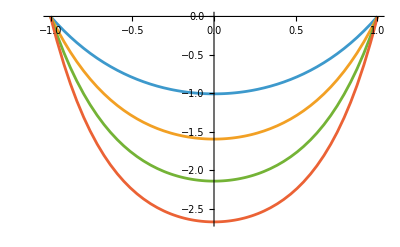

```mathematica
Plot[{catenary[3][x],catenary[4][x],catenary[5][x],catenary[6][x]},{x,-1,1}]
```

Proof: Assuming the solution correct, we first determine the coefficient a. It is plain that y[-s]=y[s]=0. We have:

ẏ= Sinh[t/a]

The arc length is:

B[y]=∫_-s^s √(1+(ẏ)^2)ⅆt
=∫_-s^s √(1+(Sinh[t/a])^2)ⅆt
=∫_-s^s Cosh[t/a]ⅆt=2a Sinh[s/a]=c

We now derive the solution. The Lagrangian is:

L_A[x,ẋ]=y √(1+(ẏ)^2)

To take account for the constraint, we add:

L_B[x,ẋ]=-λ √(1+(ẏ)^2)

and get:

L[x,ẋ]=(y-λ)√(1+(ẏ)^2)

We apply the Beltrami identity:

L-ẏ∂_(ẋ) L = L-ẏ((y-λ)ẏ)/(√(1+(ẏ)^2))

= (y-λ)√(1+(ẏ)^2)-  ((y-λ)(ẏ)^2)/(√(1+(ẏ)^2)) =(y-λ)/(√(1+(ẏ)^2))

and obtain  the differential equation:

(y-λ)/(√(1+(ẏ)^2))  =a, ẏ=√(((y-λ)/a)^2-1)

for some constant a. Separation of variables gives:

∫ⅆy/(√(((y-λ)/a)^2-1))=∫ⅆx

Setting z=(y - λ)/a (and  ⅆy=a ⅆz) gives:

∫aⅆz/(√(z^2-1))=x - b

for some constant b, so:

ArcCosh[z]=(x-b)/a

z= Cosh[(x-b)/a]=(y-λ)/a

y=a Cosh[(x-b)/a]+λ

We have b=0 because y[-s]=y[s].

#### Snell’s Law

The speed of light depends on the medium. We are given two regions R_0, R_1 and two velocities v_(0,)v_1 indicating the speed of light on each of them.
To get from (0 | 0) to (2 | 2), the light will take the path that minimizes the travel time T[a] which depends on the point (1 | y) where the light passes from R_0 to region R_1.

T[y]=(√(1+y^2))/v_0+(√(1+(2-y)^2))/v_1

ⅆ/ⅆy T[y]=y/(v_0 √(1+y^2))-(2-y)/(v_1 √(1+(2-y)^2))=0

=Sin[θ_0]/v_0-Sin[θ_1]/v_01

So:

Sin[θ_0]/v_0=Sin[θ_1]/v_1

Generalizing the above we consider n regions R_0,..,R_(n-1) and n velocities v_(0,)..,v_(n-1) indicating the speed of light on each of them. To get from (0 | 0) to (x_n | y_n), the light will take the path that minimizes the travel time T[y_1,..,y_n] which depends on the points ((x_j | y)_j) where the light passes from R_(j-1) to region R_j.

T[y]=  ∑_(j=0)^(n-1) (√((x_(j+1)-x_j)^2+(y_(j+1)-y_j)^2))/v_j

∂_j T[y]=(y_j-y_(j-1))/(v_(j-1)√((x_j-x_(j-1))^2+(y_j-y_(j-1))^2))-(y_(j+1)-y_j)/(v_j √((x_(j+1)-x_j)^2+(y_(j+1)-y_j)^2))=0

So:

Sin[θ_(j-1)]/(v_j-1) =Sin[θ_j]/v_j

and:

Sin[θ_0]/v_0=..=Sin[θ_j]/v_j =..=Sin[θ_(n-1)]/(v_(n-1))

Generalizing the above we consider a scalar function f:ℝ^n→ℝ which, for each point x, gives the action f[x] required to pass through x. What was 1/v in the previous example is now f. We want to compute a path γ from a to b that minimizes the action along that path. We assume that γ is given by a function x : [0, s] ->ℝ^n with x[0]=a, x[s]=b. The total action to be minimized is:

A[x]=  ∑_(j=0)^(n-1) f[x_j]‖x_(j+1)-x_j‖=∑_(j=0)^(n-1) f[x_j](‖x_(j+1)-x_j‖)/(t_(j-1)-t_j)(t_(j-1)-t_j)
≈∫_0^s f[x[t]]‖ẋ[t]‖ⅆt

With the Lagrangian

L[x,ẋ]=f[x]‖ẋ‖

we get

L_x=∂f[x]‖ẋ‖

L_(ẋ)=f[x](ẋ)/(‖ẋ‖)

ⅆ/ⅆt L_(ẋ)=∂f[x](ẋ)^2/(‖ẋ‖)+f[x](ẋ-x (ẋ x^(..))/(‖ẋ‖)^2)

and the Euler-Lagrange equation

∂f[x](‖ẋ‖)^2=∂f[x](ẋ)^2+f[x]‖ẋ‖(ẋ-x (ẋ x^(..))/(‖ẋ‖)^2)
∂f[x]((‖ẋ‖)^2-           =∂f[x](ẋ)^2+f[x]‖ẋ‖(ẋ-x (ẋ x^(..))/(‖ẋ‖)^2)

todo: Polarkoordinaten; f=1 -> Gerade als kürzesten Weg.

### Magnetic Field

The Lagrangian is

L[x,ẋ]=1/2 m(ẋ)^2+e ẋ A[x]

where A:ℝ^3→ℝ^3 is the vector potential, m the mass and e the charge of the moving particle. We introduce

B= ∂×A

as the magnetic field and the Lorentz force F exerted on a particle of charge e as

F=-e (ẋ×B) =-e ∂_x (ẋ A[x])

The Euler - Lagrange equation for magnetic fields is:

m x^(..)=-e (ẋ×B)

Proof: We compute the components:

∂_x L=e∂_x (ẋ A[x])=e ẋ DA[x]ᵀ
∂_(ẋ) L=m ẋ+e∂_(ẋ) (ẋ A[x])=m ẋ+e A[x]
ⅆ/ⅆt ∂_(ẋ) L=m x^(..)+e ẋ DA[x]

and plug them into Euler-Lagrange:

ⅆ/ⅆt ∂_(ẋ) L=∂_x L
m x^(..)+e ẋ DA[x]=e ẋ DA[x]ᵀ
m x^(..)=e ẋ(DA[x]ᵀ- DA[x])

Setting

G =DA[x]ᵀ- DA[x]=(. | . | .
. | ∂_i A_j-∂_j A_i | .
. | . | . )_(i=1,..,n
j=1,..,n)=(0 | B_3 | -B_2
-B_3 | 0 | B_1
B_2 | -B_1 | 0)

we get:

m x^(..)=-e G ẋ=-e ẋ×B

Same procedure with indices: We compute the components

L[x,ẋ]=m/2∑_(j=1)^n OverDot[x_j]^2+e∑_(j=1)^n (ẋ)_j A_j[x]
∂_x_i L=e∑_(j=1)^n (ẋ)_j∂_i A_j[x]         (i=1,..,n)
∂_((ẋ)_i) L=m (ẋ)_i+e A_i[x]            (i=1,..,n)
ⅆ/ⅆt ∂_((ẋ)_i) L=m(x^(..))_i+e ∑_(j=1)^n (ẋ)_j∂_j A_i[x]=e∑_(j=1)^n (ẋ)_j∂_i A_j[x]

and plug them into Euler-Lagrange:

m(x^(..))_i=e∑_(j=1)^n (ẋ)_j∂_i A_j[x]-e ∑_(j=1)^n (ẋ)_j∂_j A_i[x]
=e∑_(j=1)^n (ẋ)_j(∂_i A_j[x]-∂_j A_i[x])   (i=1,..,n)

>>> todo

We are given a medium where the speed (of light or anything else) at point x is given by v[x].
We are to find a path ϕ from (0
0) to (1
1) that minimizes the travelling time T[ϕ].

T[ϕ]= ∫_γ ⅆs/v=∫_0^s (‖ϕ̇[t]‖)/v[ϕ[t]]ⅆt

A[ϕ]= ∫_γ aⅆs=∫_0^s a[ϕ[t]]‖ϕ̇[t]‖ⅆt